# Impact of Urban Design on Quality of Life

## Intro

Most of the population around the globe is now concentrated in cities. There are around 2 dozens urban areas with populations exceeding 10 million people, but we still fail to quantify the influence of various aspects of urban design on the quality of life.
This work is a stepping stone in that direction.

## What is quality of life?

This is a very non-trivial question and we are not going to answer it in this work. Instead we will define a very simple approximation of quality of life as average sentiment across Tweets related to that specific city.

```mathematica
EstimateSentimentWL[sentence_String] := Module[{probs, pPos, pNeu, pNeg, resultPositivness, resultCertainity},
	probs = Classify["Sentiment", sentence, "Probabilities"];
	pPos = Lookup[probs, "Positive"];
	pNeu = Lookup[probs, "Neutral"];
	pNeg = Lookup[probs, "Negative"];
	resultPositivness = (pPos + pNeu * 0.5);
	resultCertainity = Max[probs];
	{resultPositivness,resultCertainity}
];
EstimateSentiments[sentences_, func_] := Map[({#, func[#]}) &, sentences];
EstimateSentiments[sentences_] := EstimateSentiments[sentences, EstimateSentimentWL];
```

## Which regions are we going to analyze?

rer

```mathematica
constantCountCities = 100;
constantDirectory = "/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts";
constantPathTweets = StringJoin[{constantDirectory, "/Tweets"}];
constantPathMaps = StringJoin[{constantDirectory, "/Maps"}];
constantCountries = {Entity["Country","UnitedStates"],Entity["Country","UnitedKingdom"],Entity["Country","Canada"],Entity["Country","Australia"],Entity["Country","NewZealand"]};
```

```mathematica
CityName[city_] := EntityValue[city, "Name"];
```

```mathematica
(* 
Ordered list of cities: https://www.timeout.com/things-to-do/best-cities-in-the-world 
Other lists can be found in "CitiesLists.nb".
*)
citiesPopular = {
Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Melbourne","Victoria","Australia"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Entity["City",{"LosAngeles","California","UnitedStates"}],Entity["City",{"Montreal","Quebec","Canada"}],Entity["City",{"Berlin","Berlin","Germany"}],Entity["City",{"Glasgow","GlasgowCity","UnitedKingdom"}],Entity["City",{"Paris","IleDeFrance","France"}],Entity["City",{"Tokyo","Tokyo","Japan"}],
Entity["City",{"Madrid","Madrid","Spain"}],Entity["City",{"CapeTown","WesternCape","SouthAfrica"}],Entity["City",{"LasVegas","Nevada","UnitedStates"}],Entity["City",{"MexicoCity","DistritoFederal","Mexico"}],Entity["City",{"Manchester","NewHampshire","UnitedStates"}],Entity["City",{"Philadelphia","Pennsylvania","UnitedStates"}],Entity["City",{"Barcelona","Barcelona","Spain"}],Entity["City",{"BuenosAires","BuenosAires","Argentina"}],Entity["City",{"Lisbon","Lisboa","Portugal"}],Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}],
Entity["City",{"TelAvivYafo","TelAviv","Israel"}],Entity["City",{"Bombay","Maharashtra","India"}],Entity["City",{"Toronto","Ontario","Canada"}],Entity["City",{"Birmingham","Alabama","UnitedStates"}],Entity["City",{"Dublin","Dublin","Ireland"}],Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}],Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"Porto","Norte","Portugal"}],Entity["Country","Singapore"],Entity["City",{"Edinburgh","Edinburgh","UnitedKingdom"}],
Entity["City",{"SanFrancisco","California","UnitedStates"}],Entity["City",{"Dubai","Dubai","UnitedArabEmirates"}],Entity["City",{"Munich","Bavaria","Germany"}],Entity["City",{"Vienna","Vienna","Austria"}],Entity["City",{"Shanghai","Shanghai","China"}],Entity["City",{"Moscow","Moscow","Russia"}],Entity["City",{"Delhi","Delhi","India"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"Sydney","NewSouthWales","Australia"}],Entity["City",{"AbuDhabi","AbuDhabi","UnitedArabEmirates"}],
Entity["City",{"HongKong","HongKong","HongKong"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"RioDeJaneiro","RioDeJaneiro","Brazil"}],Entity["City",{"Marseille","ProvenceAlpesCoteDAzur","France"}],Entity["City",{"Bangkok","Bangkok","Thailand"}],Entity["City",{"KualaLumpur","KualaLumpur","Malaysia"}],Entity["City",{"Beijing","Beijing","China"}],Entity["City",{"Istanbul","Istanbul","Turkey"}]
};
```

```mathematica
tw = ServiceConnect["Twitter"];
TwPath[city_String] := StringJoin[{constantPathTweets, "/", city, ".mx"}];
TwDownloadCity[city_] := Module[{name, data, path},
	name = CityName[city];
	path = TwPath[name];
	data = tw["TweetSearch", "Query"->name];
	Export[path, data, OverwriteTarget->True];
	data
];
TwPullCity[city_] := Module[{name, data, path},
	name = CityName[city];
	path = TwPath[name];
	data = If[FileExistsQ[path], Import[path], TwDownloadCity[city]];
	Normal[data]
];
```

```mathematica
EstimateQualityOfLife[city_] := Module[{data, tweetsWSentiments, sentimentsWCertainity, meanPositivness, meanCertainty},
	data = TwPullCity[city];
	data = data⟦All, "Text"⟧;
	tweetsWSentiments = EstimateSentiments[data];
	sentimentsWCertainity = tweetsWSentiments⟦All, 2⟧;
	meanPositivness = MeanAround[sentimentsWCertainity⟦All, 1⟧];
	meanCertainty = MeanAround[sentimentsWCertainity⟦All, 2⟧];
	meanPositivness
];
```

```mathematica
Map[TwDownloadCity, citiesPopular];
```

```mathematica
citiesQuality = Map[EstimateQualityOfLife, citiesPopular];
```

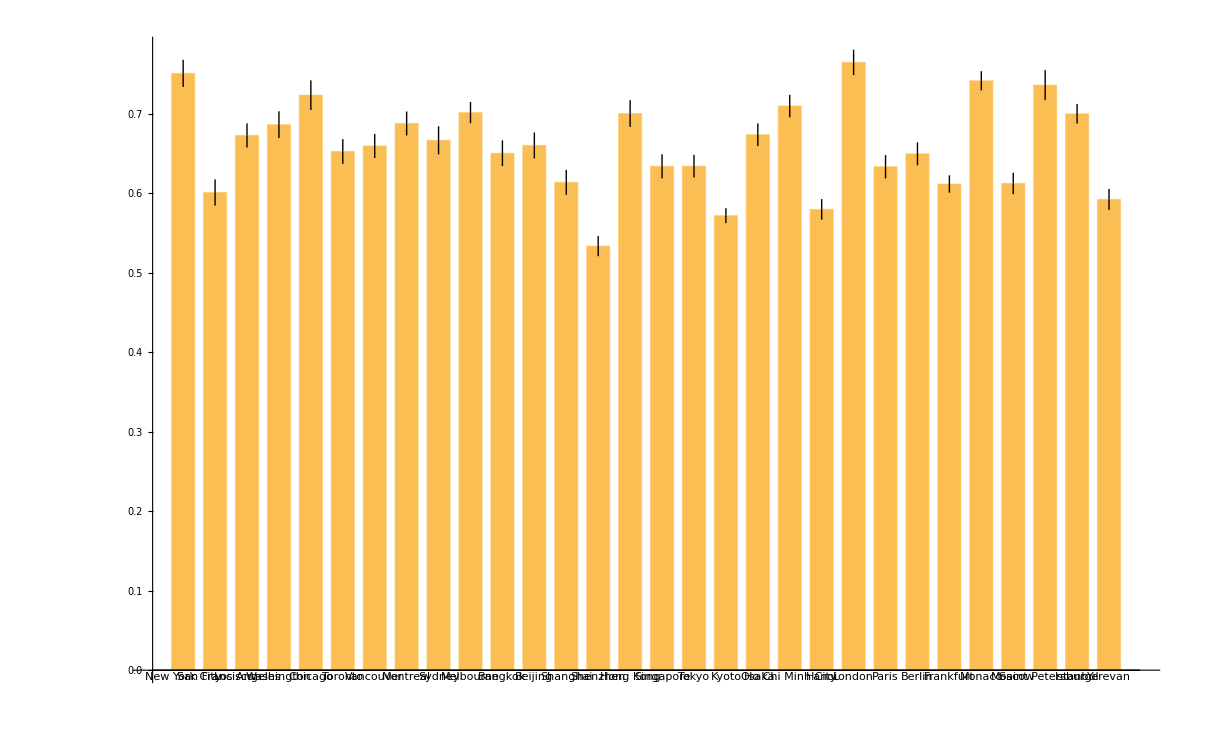

```mathematica
BarChart[citiesQuality,ChartLabels->Map[CityName, citiesPopular]]
```

## Are there any correlations at all?

wew

```mathematica
ExtractCityStatsFeatures[city_]:=Module[{}, 
	
];
ExtractCountryStatsFeatures[city_];
ExtractMapFeatures[city_];
```

## Are there correlations between cities topology and quality of life?

wewe

## Are there correlations between known features and quality of life?

wewe